# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Spin transport\\Quantum channel\\QMB_offline.wl"]
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14];
```

# Ising chaometer

```mathematica
J=1;
h=1.05;
L=8;
g=0.5;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
Ha=IsingHamiltonian[1,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=1;
Lb=L-La;
sdiageigenvec=ParallelTable[sdiag[L,La,Lb,i],{i,allvecs},DistributedContexts->Full];
```

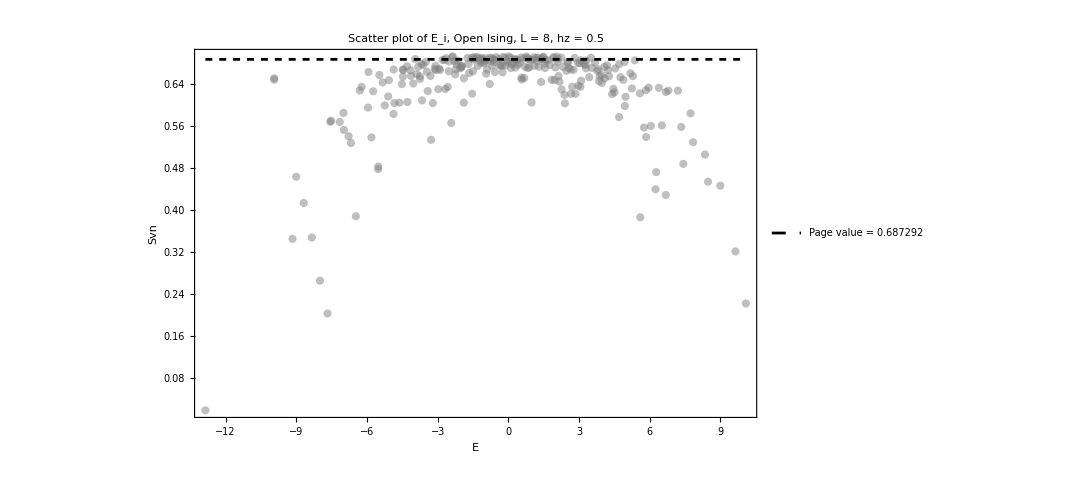

```mathematica
Show[{ListPlot[Transpose[{allvals,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Open Ising, L = "<>ToString[L]<>", hz = "<>ToString[g]<>"",35,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->800,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[allvals],Max[allvals]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

```mathematica
productstate2=Table[RandomChainProductState[L],10];
(*productstate2=Table[Flatten[KroneckerProduct[haar[1],haar[L-1]]],50];*)
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].Ha.i],{i,productstate2},DistributedContexts->Full];
```

```mathematica
data=SortBy[Transpose[{iprs,energies,productstate2}],First];
productstate=data[[1;;5]][[All,3]];
```

```mathematica
tlist=Table[i,{i,0,200,0.05}];
tlist//Length
```

4001

```mathematica
fakesvn=Table[ParallelTable[{t,pur[L,La,Lb,i,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

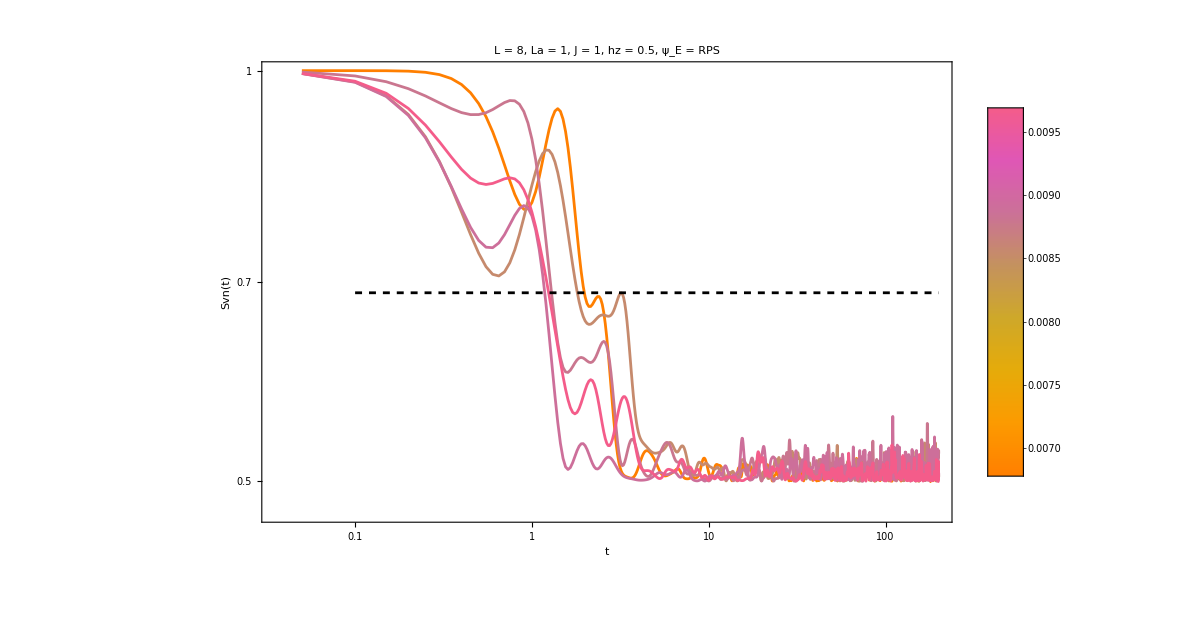

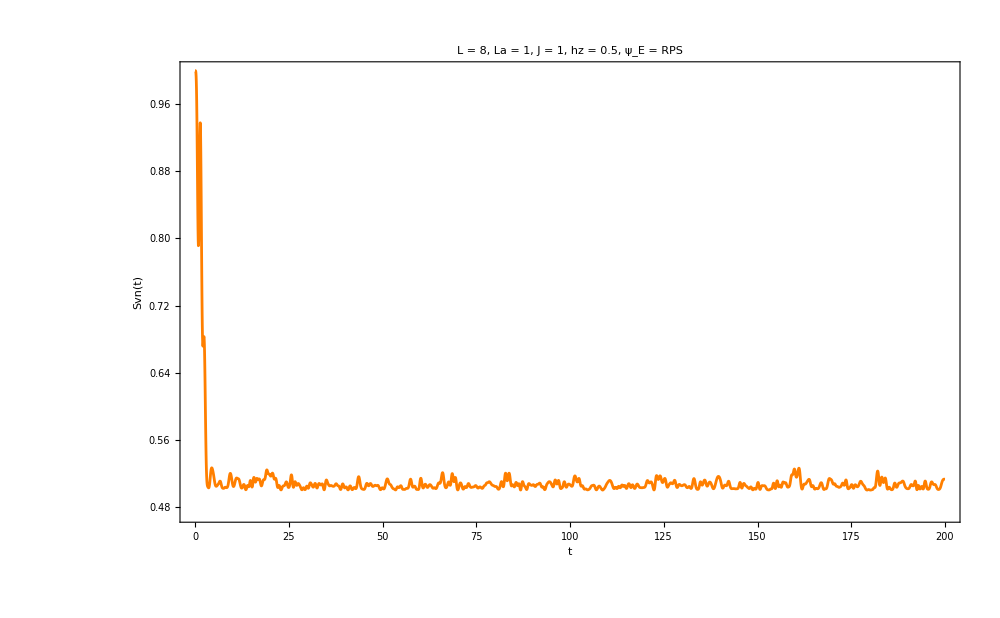

```mathematica
(*Step 1:Determine the overall energy range*)
sorted=data[[1;;5]][[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
(*Step 2:Define a function to map an energy value to a temperature-like color*)
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListLogLogPlot[fakesvn[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}];
Legended[Show[{plots,LogLogPlot[pageEntropy[La,Lb],{x,10^-1,Max[tlist]},PlotStyle->{Directive[Black,Dashed]}]}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
i=1;
ListPlot[fakesvn[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]]
```

# Choi matrix ising

## Test old

```mathematica
i=1;
ψ=productstate[[i]];
rho=Chop[MatrixPartialTrace[Dyad[ψ],1,{2^La,2^Lb}]];
```

```mathematica
{L,La,Lb}
ψ//Dimensions
rho//Dimensions
```

{5,1,4}

{32}

{16,16}

```mathematica
A=KroneckerProduct[IdentityMatrix[2^(Lb)]/2^(La),rho];
P=Transpose[allvecs];
Pinv=Conjugate[allvecs];
```

```mathematica
A//Dimensions
allvecs//Dimensions
```

{256,256}

{32,32}

```mathematica
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*allvals*t]].Pinv;
```

```mathematica
AbsoluteTiming[chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist}];
truepurity=Chop[Map[Tr,Map[#.#&,chois]]];]
```

{12.0477,Null}

```mathematica
chois[[1]]//Dimensions
```

{4,4}

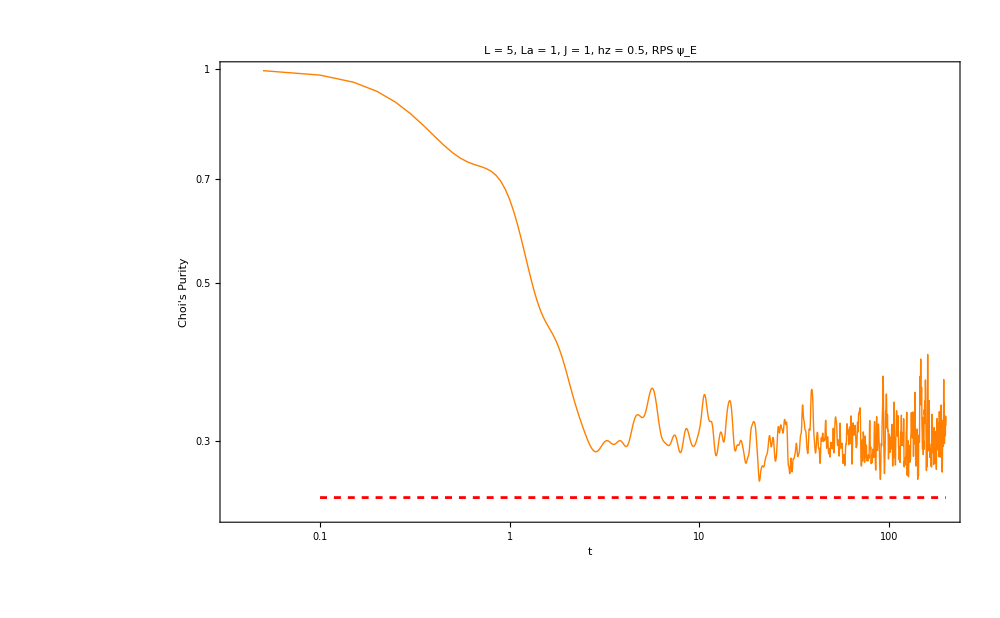

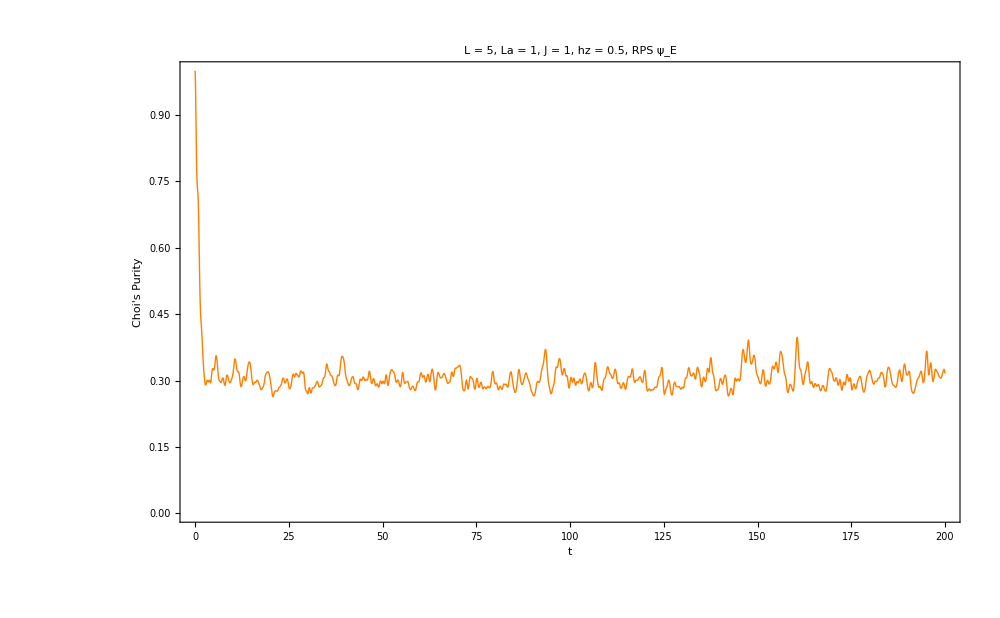

0.307297

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,truepurity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]],Thick]];
final=Show[{plot,LogLogPlot[1/((2^La)^2),{x,10^-1,tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]}]
ListPlot[Transpose[{tlist,truepurity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]],Thick]]
decoherence[truepurity,tlist]
```

## Improved code c

```mathematica
Needs["Developer`"];
ClearAll[PackC];
PackC[x_]:=Developer`ToPackedArray[x];
(*1) Environment state from a global pure state|ψ⟩ on S⊗E*)
ClearAll[EnvStateFromPsi];
EnvStateFromPsi[psi_,m_Integer?Positive,n_Integer?Positive]:=PackC@Chop@MatrixPartialTrace[Dyad[psi],1,{m,n}];
(*2) Fast spectral unitary builder:U(t)=V.diag(e^{-i λ t}).V^†,implemented via column scaling (no DiagonalMatrix allocation)*)
ClearAll[SpectralUnitary];
SpectralUnitary[allvecs_,allvals_]:=Module[{P=PackC@Transpose[allvecs],Pinv=PackC@Conjugate[allvecs]},Function[{t},With[{ph=PackC@Exp[-I allvals t]},PackC@(Transpose[Transpose[P]*ph].Pinv)]]];
ClearAll[PhiProjector];
PhiProjector[m_Integer?Positive]:=Module[{phi=PackC@(Flatten[IdentityMatrix[m]]/Sqrt[m])},PackC@Dyad[phi]];
ClearAll[ChoiSysBuilder];
Options[ChoiSysBuilder]={"rhoE"->None,"psi"->None};
ChoiSysBuilder[m_Integer?Positive,n_Integer?Positive,unitaryF_Function,opts:OptionsPattern[]]:=Module[{rhoE=OptionValue["rhoE"],psi=OptionValue["psi"],projPhi,idm},If[rhoE===None&&psi===None,Message[ChoiSysBuilder::envspec];Return[$Failed]];
If[rhoE=!=None&&psi=!=None,Message[ChoiSysBuilder::envboth];Return[$Failed]];
rhoE=If[rhoE===None,EnvStateFromPsi[psi,m,n],rhoE]//PackC;
projPhi=PhiProjector[m];
idm=IdentityMatrix[m,SparseArray];(*sparse identity*)Function[{t},Module[{U=unitaryF[t],UR,Omega,X},UR=KroneckerProduct[idm,U];(*acts on R⊗S⊗E*)Omega=KroneckerProduct[projPhi,rhoE];(* |Φ⟩⟨Φ|⊗ρE*)X=UR.Omega.ConjugateTranspose[UR];
PackC@Chop@MatrixPartialTrace[X,3,{m,m,n}]]]];

ChoiSysBuilder::envspec="Provide either \"rhoE\" -> (n×n matrix) or \"psi\" -> (mn-vector).";
ChoiSysBuilder::envboth="Provide only one of \"rhoE\" or \"psi\", not both.";

ClearAll[ProcessPurity];
Options[ProcessPurity]={"Parallel"->True};
ProcessPurity[choiF_Function,tlist_List,OptionsPattern[]]:=Module[{par=TrueQ[OptionValue["Parallel"]]},If[par,ParallelMap[(Chop@Re@Tr[#.#])&@*choiF,tlist,Method->"CoarsestGrained"],Map[(Chop@Re@Tr[#.#])&@*choiF,tlist]]];
```

```mathematica
m=2^La;
n=2^Lb;
i=1;
ψ=productstate[[i]];
(*Option A:environment given as a pure global state|ψ⟩*)
rhoE=EnvStateFromPsi[ψ,m,n];
unitaryF=SpectralUnitary[allvecs,allvals];
choiF=ChoiSysBuilder[m,n,unitaryF,"rhoE"->rhoE];
```

```mathematica
(*Purity over your tlist*)
AbsoluteTiming[purity=ProcessPurity[choiF,tlist];]
```

{329.35,Null}

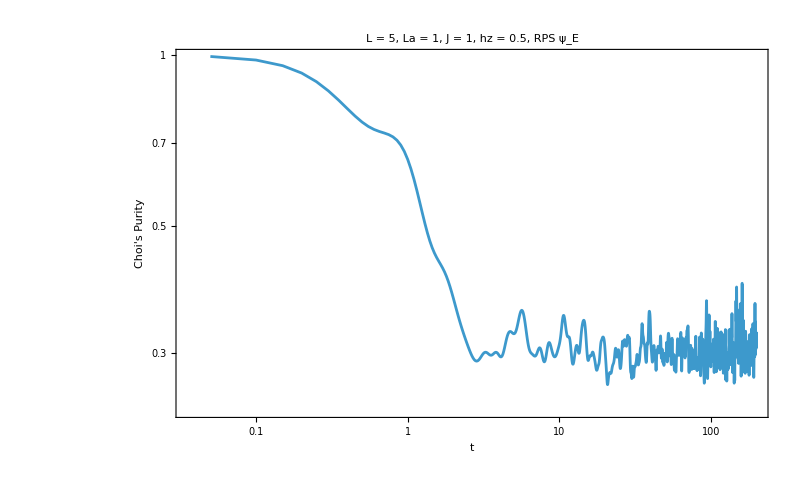

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->800]
```

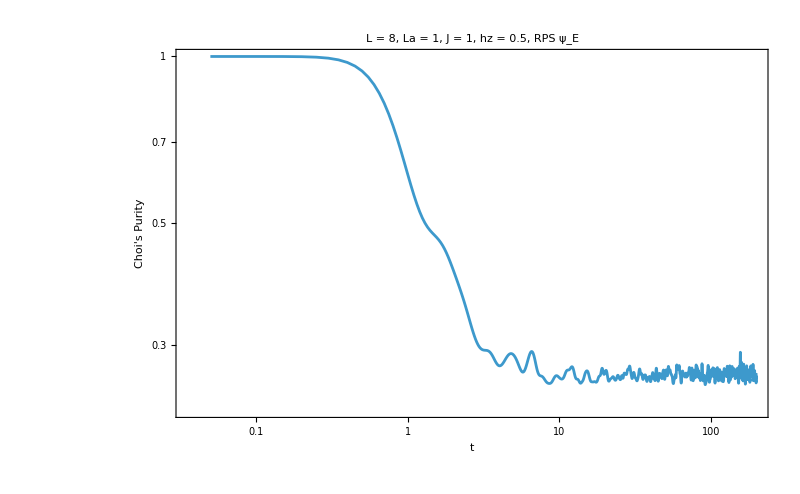

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->800]
```

# Spin chain

```mathematica
(* ============================================================
   PARAMETERS
   ============================================================ *)
nChain = 4;          (* number of chain spins                  *)
nTotal = nChain + 2; (* +2 for the two boundary system spins   *)

(* site 1 = S_A,  sites 2..nChain+1 = chain,  site nTotal = S_B *)
siteA = 1;
siteB = nTotal;
chainSites = Range[2, nChain + 1];

(* ============================================================
   PAULI MATRICES AND SINGLE-SITE OPERATORS
   ============================================================ *)
id2 = IdentityMatrix[2];
sx  = {{0, 1}, {1, 0}}/2;
sy  = {{0, -I}, {I, 0}}/2;
sz  = {{1, 0}, {0, -1}}/2;

(* Embed a 2x2 operator at site k in the full 2^nTotal Hilbert space *)
siteOp[op_, k_] := KroneckerProduct @@ ReplacePart[
  Table[id2, nTotal],
  k -> op
];
```

```mathematica
(* ============================================================
   HAMILTONIAN
   ============================================================ *)
(* --- Local fields (customize hA, hB, hChain as needed) --- *)
hA     = 1;    (* field on S_A          *)
hB     = 1;    (* field on S_B          *)
hChain = 0.5;  (* uniform field on chain *)

HAlocal = hA * siteOp[sz, siteA];
HBlocal = hB * siteOp[sz, siteB];

HChainlocal = Sum[hChain * siteOp[sz, k], {k, chainSites}];
```

```mathematica
(* --- Nearest-neighbor chain Heisenberg interactions --- *)
(* J_chain between adjacent chain spins *)
jChain = 1;
HChainint = Sum[
  jChain * (
    siteOp[sx, k] . siteOp[sx, k+1] +
    siteOp[sy, k] . siteOp[sy, k+1] +
    siteOp[sz, k] . siteOp[sz, k+1]
  ),
  {k, chainSites[[1 ;; -2]]}  (* pairs within chain *)
];
```

```mathematica
(* --- System-chain boundary coupling --- *)
(* S_A couples to first chain site, S_B to last *)
jBoundary = 0.5;
HAcouple = jBoundary * (
  siteOp[sx, siteA] . siteOp[sx, chainSites[[1]]] +
  siteOp[sy, siteA] . siteOp[sy, chainSites[[1]]] +
  siteOp[sz, siteA] . siteOp[sz, chainSites[[1]]]
);
HBcouple = jBoundary * (
  siteOp[sx, siteB] . siteOp[sx, chainSites[[-1]]] +
  siteOp[sy, siteB] . siteOp[sy, chainSites[[-1]]] +
  siteOp[sz, siteB] . siteOp[sz, chainSites[[-1]]]
);

HFull = HAlocal + HBlocal + HChainlocal + HChainint + HAcouple + HBcouple;
```

```mathematica
(* ============================================================
   FULL DENSITY MATRIX (thermal state at inverse temperature β)
   ============================================================ *)
β = 1;

(* Partition function and thermal state *)
rhoFull = MatrixExp[-β * HFull];
rhoFull = rhoFull / Tr[rhoFull];
```

```mathematica
(* ============================================================
   PARTIAL TRACE OVER THE CHAIN
   Retain sites siteA and siteB, trace out chainSites
   ============================================================ *)

(* 
   Tensor structure: site1 ⊗ site2 ⊗ ... ⊗ siteN
   We want to trace over indices {2, ..., nChain+1}.
   
   Reshape the density matrix into a rank-2*nTotal tensor,
   then contract the chain indices.
*)

dim = 2^nTotal;
dimAB  = 4;                  (* 2^2: only two system spins kept *)
dimEnv = 2^nChain;           (* chain Hilbert space dimension   *)

(* 
   Reshape: rho[i1,i2,...,iN, j1,j2,...,jN]  (each index ∈ {1,2})
   Standard tensor index ordering: site 1 is leftmost (fastest-varying last)
*)
rhoTensor = ArrayReshape[rhoFull, Join[Table[2, 2*nTotal]]];
```

```mathematica
(* 
   Trace over chain sites.
   After reshaping, index positions for sites:
     ket side: site k -> position k
     bra side: site k -> position k + nTotal
   
   Contract chain indices: for each chain site k, sum over
   index k = index (k + nTotal), leaving siteA and siteB.
*)
contractedIndices = Transpose[{chainSites, chainSites + nTotal}];
```

```mathematica
rhoABtensor = rhoTensor;
(* Contract one pair at a time; each contraction reduces rank by 2 *)
offset = 0;
Do[
  (* Adjust positions after previous contractions *)
  k1 = contractedIndices[[i, 1]] - offset;
  k2 = contractedIndices[[i, 2]] - offset;

  (* TensorContract: set index k1 = index k2 and sum *)
  rhoABtensor = TensorContract[rhoABtensor, {k1, k2}];
  offset += 2;  (* rank decreased by 2 per contraction *)
  ,
  {i, Length[contractedIndices]}
];
```

TensorContract::contr: Invalid contraction 0.

TensorContract::contr: Invalid contraction 6.

General::stop: Further output of TensorContract::contr will be suppressed during this calculation.

```mathematica
(* Final reshape: 4x4 matrix for the two-spin system *)
rhoAB = ArrayReshape[rhoABtensor, {dimAB, dimAB}];

(* Verify trace = 1 *)
Print["Tr[rhoAB] = ", Tr[rhoAB]]     (* should be 1 *)
Print["Hermitian: ", HermitianMatrixQ[rhoAB, Tolerance -> 1*^-10]]
Print["rhoAB = "];
rhoAB // MatrixForm
```

ArrayReshape::listrp: List, SparseArray object, or structured array expected at position 1 in ArrayReshape[TensorContract[TensorContract[{{{{{«2»},{«2»}},{{«2»},{«2»}}},{{{«2»},{«2»}},{{«2»},{«2»}}}},{{{{«2»},{«2»}},{{«2»},{«2»}}},{{{«2»},{«2»}},{{«2»},{«2»}}}}},{0,6}],{-1,5}],{4,4}].

Tr[rhoAB] = Tr[ArrayReshape[TensorContract[TensorContract[{{{{{{{{0.00241524,0.},{0.,0.}},{{0.,0.},{0.,0.}}},{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}},{{{{0.,0.00870021},{-0.00221949,0.}},{{0.00057097,0.},{0.,0.}}},{{{-0.000173401,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}},{{{{{0.,-0.00222093},{0.00982955,0.}},{{-0.00488186,0.},{0.,0.}}},{{{0.00209825,0.},{0.,0.}},{{0.,0.},{0.,0.}}}},{{{{0.,0.},{0.,0.0207201}},{{0.,-0.0135442},{0.00135072,0.}}},{{{0.,0.00629229},{-0.000954625,0.}},{{0.000100434,0.},{0.,0.}}}}}},{{{{{{0.,0.000583645},{-0.00497989,0.}},{{0.0119935,0.},{0.,0.}}},{{{-0.00862619,0.},{0.,0.}},{{0.,0.},{0.,0.}}}},{{{{0.,0.},{0.,-0.0138096}},{{0.,0.042137},{-0.00632487,0.}}},{{{0.,-0.0307436},{0.00641038,0.}},{{-0.000844824,0.},{0.,0.}}}}},{{{{{0.,0.},{0.,0.00137619}},{{0.,-0.00632715},{0.0149308,0.}}},{{{0.,0.00536488},{-0.0187414,0.}},{{0.00377641,0.},{0.,0.}}}},{{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.0302436}}},{{{0.,0.},{0.,-0.0384549}},{{0.,0.00924393},{-0.000602687,0.}}}}}}},{{{{{{{0.,-0.0000779637},{0.000918456,0.}},{{-0.00358172,0.},{0.,0.}}},{{{0.0142312,0.},{0.,0.}},{{0.,0.},{0.,0.}}}},{{{{0.,0.},{0.,0.00274056}},{{0.,-0.0127572},{0.00220237,0.}}},{{{0.,0.0512169},{-0.0126911,0.}},{{0.00236382,0.},{0.,0.}}}}},{{{{{0.,0.},{0.,-0.00040845}},{{0.,0.00263172},{-0.00759432,0.}}},{{{0.,-0.0126896},{0.0538735,0.}},{{-0.0169968,0.},{0.,0.}}}},{{{{0.,0.},{0.,0.}},{{0.,0.},{0.,-0.0155715}}},{{{0.,0.},{0.,0.112365}},{{0.,-0.044938},{0.00387187,0.}}}}}},{{{{{{0.,0.},{0.,0.0000415755}},{{0.,-0.000336177},{0.00147397,0.}}},{{{0.,0.00235115},{-0.0168988,0.}},{{0.0247598,0.},{0.,0.}}}},{{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.00359315}}},{{{0.,0.},{0.,-0.0446725}},{{0.,0.0860658},{-0.0124779,0.}}}}},{{{{{0.,0.},{0.,0.}},{{0.,0.},{0.,-0.000229868}}},{{{0.,0.},{0.,0.00384641}},{{0.,-0.0124756},{0.0284925,0.}}}},{{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}},{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.0576433}}}}}}}},{0,6}],{-1,5}],{4,4}]]

Hermitian: False

rhoAB =

ArrayReshape[TensorContract[TensorContract[{{{{{{{{0.00241524,0.},{0.,0.}},{{0.,0.},{0.,0.}}},{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}},{{{{0.,0.00870021},{-0.00221949,0.}},{{0.00057097,0.},{0.,0.}}},{{{-0.000173401,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}},{{{{{0.,-0.00222093},{0.00982955,0.}},{{-0.00488186,0.},{0.,0.}}},{{{0.00209825,0.},{0.,0.}},{{0.,0.},{0.,0.}}}},{{{{0.,0.},{0.,0.0207201}},{{0.,-0.0135442},{0.00135072,0.}}},{{{0.,0.00629229},{-0.000954625,0.}},{{0.000100434,0.},{0.,0.}}}}}},{{{{{{0.,0.000583645},{-0.00497989,0.}},{{0.0119935,0.},{0.,0.}}},{{{-0.00862619,0.},{0.,0.}},{{0.,0.},{0.,0.}}}},{{{{0.,0.},{0.,-0.0138096}},{{0.,0.042137},{-0.00632487,0.}}},{{{0.,-0.0307436},{0.00641038,0.}},{{-0.000844824,0.},{0.,0.}}}}},{{{{{0.,0.},{0.,0.00137619}},{{0.,-0.00632715},{0.0149308,0.}}},{{{0.,0.00536488},{-0.0187414,0.}},{{0.00377641,0.},{0.,0.}}}},{{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.0302436}}},{{{0.,0.},{0.,-0.0384549}},{{0.,0.00924393},{-0.000602687,0.}}}}}}},{{{{{{{0.,-0.0000779637},{0.000918456,0.}},{{-0.00358172,0.},{0.,0.}}},{{{0.0142312,0.},{0.,0.}},{{0.,0.},{0.,0.}}}},{{{{0.,0.},{0.,0.00274056}},{{0.,-0.0127572},{0.00220237,0.}}},{{{0.,0.0512169},{-0.0126911,0.}},{{0.00236382,0.},{0.,0.}}}}},{{{{{0.,0.},{0.,-0.00040845}},{{0.,0.00263172},{-0.00759432,0.}}},{{{0.,-0.0126896},{0.0538735,0.}},{{-0.0169968,0.},{0.,0.}}}},{{{{0.,0.},{0.,0.}},{{0.,0.},{0.,-0.0155715}}},{{{0.,0.},{0.,0.112365}},{{0.,-0.044938},{0.00387187,0.}}}}}},{{{{{{0.,0.},{0.,0.0000415755}},{{0.,-0.000336177},{0.00147397,0.}}},{{{0.,0.00235115},{-0.0168988,0.}},{{0.0247598,0.},{0.,0.}}}},{{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.00359315}}},{{{0.,0.},{0.,-0.0446725}},{{0.,0.0860658},{-0.0124779,0.}}}}},{{{{{0.,0.},{0.,0.}},{{0.,0.},{0.,-0.000229868}}},{{{0.,0.},{0.,0.00384641}},{{0.,-0.0124756},{0.0284925,0.}}}},{{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}},{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.0576433}}}}}}}},{0,6}],{-1,5}],{4,4}]